```mathematica
ClearAll["Global`*"];
```

```mathematica
l=2;
m=1;
Clear[σ];
sol=NSolve[(1-σ^2)D[LegendreP[l,m,σ], σ]==m LegendreP[l,m,σ],σ,20];
w=2σ /. sol
```

{1.}

```mathematica
λ=Extract[w,1]
```

1.

```mathematica
σ=λ/2;
```

```mathematica
If [EvenQ[l-m],{
n=(l-m)/2;
c[i_,j_,m_,n_]=((-1)^(i+j)(2(m+n+i+j)-1)!!)/(2^(j+1)(2i-1)!!(n-i-j)!i!j!(m+j)!);
gz[s_,z_]=∑_(i=1)^n (∑_(j=0)^(n-i) c[i,j,m,n] σ^(2i-1)(1-σ^2)^j(2i)s^(m+2j)z^(2i-1));
gs[s_,z_]=∑_(i=0)^n (∑_(j=0)^(n-i) c[i,j,m,n] σ^(2i)(1-σ^2)^(j-1)(m+m σ+2j σ)s^(m+2j-1)z^(2i));
gϕ[s_,z_]=∑_(i=0)^n (∑_(j=0)^(n-i) c[i,j,m,n] σ^(2i)(1-σ^2)^(j-1)(m+m σ+2j)s^(m+2j-1)z^(2i));},
{n=(l-m-1)/2;
c[i_,j_,m_,n_]=((-1)^(i+j)(2(m+n+i+j)+1)!!)/(2^(j+1)(2i+1)!!(n-i-j)!i!j!(m+j)!);
gz[s_,z_]=∑_(i=0)^n (∑_(j=0)^(n-i) c[i,j,m,n] σ^(2i-1)(1-σ^2)^j(2i+1)s^(m+2j)z^(2i));
gs[s_,z_]=∑_(i=0)^n (∑_(j=0)^(n-i) c[i,j,m,n] σ^(2i)(1-σ^2)^(j-1)(m+m σ+2j σ)s^(m+2j-1)z^(2i+1));
gϕ[s_,z_]=∑_(i=0)^n (∑_(j=0)^(n-i) c[i,j,m,n] σ^(2i)(1-σ^2)^(j-1)(m+m σ+2j)s^(m+2j-1)z^(2i+1));}];
Us[s_,z_]=-ⅈ gs[s,z]
Uϕ[s_,z_]=gϕ[s,z]
Uz[s_,z_]=ⅈ gz[s,z]
```

-3. ⅈ z

3. z

3. ⅈ s

```mathematica
q[s_,ϕ_,z_,t_]={Us[s,z],Uϕ[s,z],Uz[s,z]}(Cos[m ϕ+λ t]+ⅈ Sin[m ϕ+λ t]);
```

```mathematica
Vs[s_,ϕ_,z_,t_]=gs[s,z]Sin[m ϕ+λ t];
Vϕ[s_,ϕ_,z_,t_]= gϕ[s,z]Cos[m ϕ+λ t];
Vz[s_,ϕ_,z_,t_]=-gz[s,z]Sin[m ϕ+λ t];
energy[s_,z_]= 1/2(gs[s,z]^2+ gϕ[s,z]^2+ gz[s,z]^2);
toten=2π NIntegrate[s energy[s,z],{s,0,1},{z,-√(1-s^2),√(1-s^2)},MinRecursion->3, MaxRecursion ->20]
normconst=√toten;

Vr[r_,θ_,ϕ_,t_]=Vs[r Sin[θ],ϕ,r Cos[θ],t]Sin[θ]+Vz[r Sin[θ],ϕ,r Cos[θ],t]Cos[θ];
Vθ[r_,θ_,ϕ_,t_]=-Vz[r Sin[θ],ϕ,r Cos[θ],t]Sin[θ]+Vs[r Sin[θ],ϕ,r Cos[θ],t]Cos[θ];
energy2[r_,θ_,ϕ_,t_]=Vr[r,θ,ϕ,t]^2+Vθ[r,θ,ϕ,t]^2+Vϕ[r Sin[θ],ϕ,r Cos[θ],t]^2;
(*toten2=NIntegrate[r^2 Sin[θ]energy2[r,θ,ϕ,0],{r,0,1},{θ,0,π},{ϕ,0,2π}]*)
```

15.0796

```mathematica
us[s_,ϕ_,z_,t_]=1/normconst gs[s,z]Sin[m ϕ+λ t];
uϕ[s_,ϕ_,z_,t_]=1/normconst gϕ[s,z]Cos[m ϕ+λ t];
uz[s_,ϕ_,z_,t_]=-1/normconst gz[s,z]Sin[m ϕ+λ t];
ur[r_,θ_,ϕ_,t_]=us[r Sin[θ],ϕ,r Cos[θ],t]Sin[θ]+uz[r Sin[θ],ϕ,r Cos[θ],t]Cos[θ];
uθ[r_,θ_,ϕ_,t_]=-uz[r Sin[θ],ϕ,r Cos[θ],t]Sin[θ]+us[r Sin[θ],ϕ,r Cos[θ],t]Cos[θ];
nenergy[s_,z_]=1/(2 toten)( gs[s,z]^2+ gϕ[s,z]^2+ gz[s,z]^2);
ntoten=2π NIntegrate[s nenergy[s,z],{s,0,1},{z,-√(1-s^2),√(1-s^2)},MinRecursion->3, MaxRecursion ->20]
```

1.

```mathematica
radius=0.33037;
sqflux1=π NIntegrate[gs[√(radius^2-z^2),z]^2(radius^2-z^2)/radius,{z,-radius,radius}];
sqflux2= 2π NIntegrate[gs[√(radius^2-z^2),z]gz[√(radius^2-z^2),z] z/radius √(radius^2-z^2),{z,-radius,radius}];
sqflux3=  π NIntegrate[gz[√(radius^2-z^2),z]^2 z^2/radius,{z,-radius,radius}];
sqflux=(sqflux1-sqflux2+sqflux3)/toten
```

0.

```mathematica
f[s_,z_]=(2s)/m(ⅈ Us[s,z]-σ Uϕ[s,z]);
```

```mathematica
p[s_,ϕ_,z_,t_]=Re[1/normconst f[s,z] ⅇ^(ⅈ (m ϕ+λ t))];
```

```mathematica
radius=1;
```

```mathematica
VectorPlot[{uϕ[radius Sin[θ],ϕ,radius Cos[θ],0], uθ[radius ,θ,ϕ,0]},{ϕ,0,2 π},{θ,0,π},VectorPoints->50,VectorScale->{0.03,Scaled[1]},VectorStyle->Blue,StreamPoints->Fine, StreamScale->None,StreamStyle->Orange,FrameLabel->{ϕ,θ},AspectRatio->0.5,ImageSize->700]
```

-Graphics-

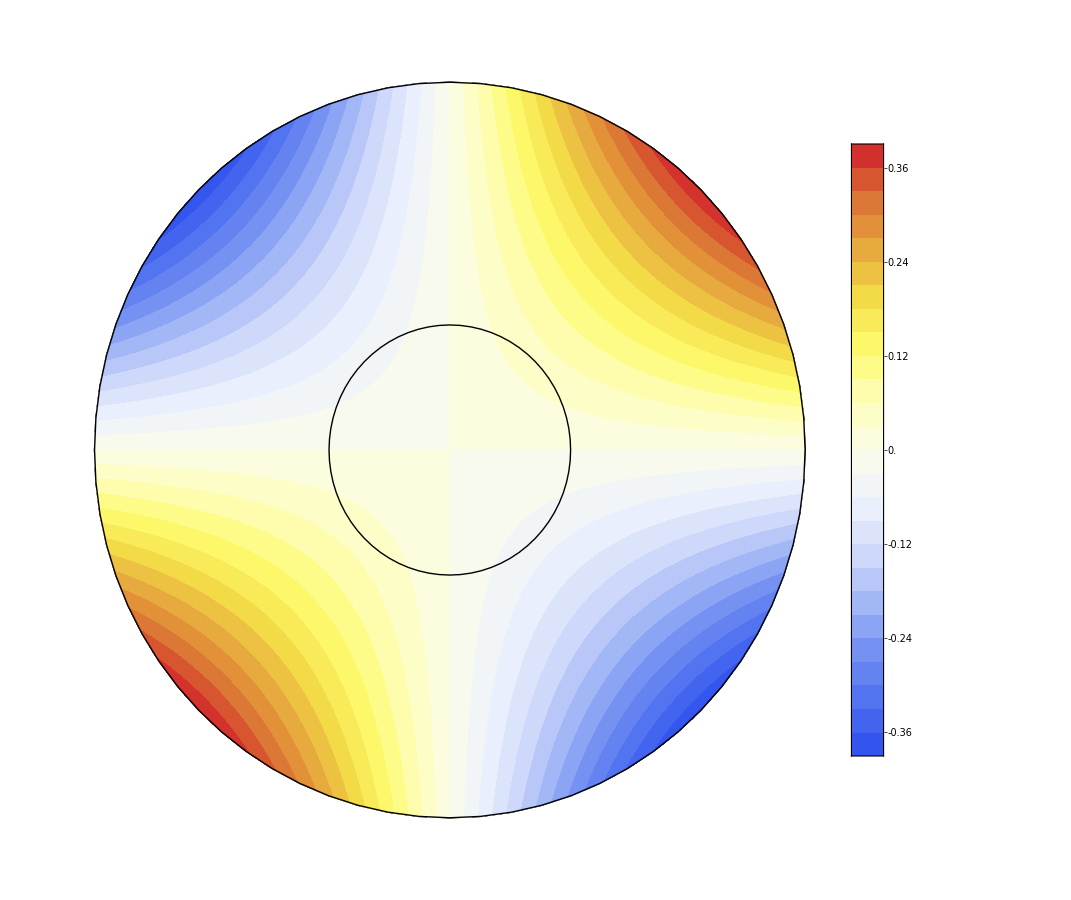

```mathematica
pres=ContourPlot[f[s,z]/normconst,{s,-1,1},{z,-1,1},Mesh->None,ContourLabels->None,Contours->50,ColorFunction->ColorData["TemperatureMap"],ContourStyle->None,RegionFunction->Function[{s,z},s^2+z^2<1],PlotLegends->Automatic,PerformanceGoal->"Quality"];core2=Graphics[{Thick,Circle[{0.0,0.0},0.34,{0,2*Pi}]}];
outer =Graphics[{Thick,Circle[{0.0,0.0},1,{0,2*Pi}]}];
Show[core2,outer,pres, core2, outer,ImageSize->900]
```

```mathematica
phi0=π/8;
t0=0;
flowm= VectorPlot[{us[s,phi0,z,t0],uz[s,phi0,z,t0]}, {s, -1, 1}, {z,-1, 1},RegionFunction->Function[{s,z},s^2+z^2<1],
VectorPoints->Fine,VectorStyle->Blue,VectorScale->{0.05,Scaled[0.9]},FrameLabel->{s,z},AspectRatio->2,PerformanceGoal->"Quality"];
contm = StreamPlot[{us[s,phi0,z,t0],uz[s,phi0,z,t0]}, {s, -1, 1}, {z,-1, 1},RegionFunction->Function[{s,z},s^2+z^2<1], StreamStyle->LightBlue, StreamScale->None,StreamPoints->Fine,PerformanceGoal->"Quality"];
Show[core2,outer, flowm,contm,ImageSize->900]
```

-Graphics-

```mathematica
ux[x_,y_,z_,t_]= us[x^2+y^2,ArcTan[x,y],z,t]Cos[ArcTan[x,y]]-uϕ [x^2+y^2,ArcTan[x,y],z,t]Sin[ArcTan[x,y]];
uy[x_,y_,z_,t_]= us[x^2+y^2,ArcTan[x,y],z,t]Sin[ArcTan[x,y]]+uϕ [x^2+y^2,ArcTan[x,y],z,t]Cos[ArcTan[x,y]];
```

```mathematica
z=0.4;
flowh= VectorPlot[{ux[x,y,z,0],uy[x,y,z,0]},{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y},x^2+y^2<1-z^2],
VectorPoints->40,VectorStyle->Blue,VectorScale->{0.05,Scaled[1]},FrameLabel->{s,z},AspectRatio->2];
conth = StreamPlot[{ux[x,y,z,0],uy[x,y,z,0]},{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y},x^2+y^2<1-z^2], StreamStyle->LightBlue, StreamScale->None,StreamPoints->Fine,PerformanceGoal->"Quality"];
Show[core2, outer, conth,flowh, ImageSize->900]
```

-Graphics-

```mathematica
ur[1,1,1,1]
```

0.